### V2

```mathematica
progress =Module[{sorted = SortBy[Select[Values[$LifeData],#Class==="Oscillator"&&KeyExistsQ[#,"Period"]&],#Year&], curr, weightsovertime,improvements,locs},
Table[
curr = Select[sorted, #Period ==i&];
weightsovertime=Times@@Dimensions[#MatrixData]&/@curr;
improvements=FoldList[Function[{min,next},If[next<min,next,min]],Infinity,weightsovertime];
locs=Select[Partition[improvements,2,1],#[[1]]!=#[[2]]&->"Index"];
curr[[locs]]
, {i, 2, 30}]];
```

```mathematica
ListPlot[ReplacePart[#, {1-> Style[#[[1]], Red], -1-> Style[#[[-1]], ColorData[96,"ColorList"][[1]]]}]&/@ 
Map[Callout[{#Year, #Period},ArrayPlot[ArrayPad[#MatrixData, 1],ImageSize->Tiny]]&, progress, {2}], PlotStyle->Directive[Lighter[Gray], PointSize[.0075]], Prolog->({Opacity[.3, Gray],HalfLine[{#Year,#Period},{-1,0}]&/@progress[[All, -1]]}), PlotRange->{{1969, 2025}, {2, 30}}, AspectRatio->.4, Frame-> True]
```

-Graphics-

### Trying to improve callout plot

Variable heights is a nightmare because it messes with the alignment of the year!! The only way to fix this is to stretch the plot out which will look weird.

But I got it to work, now just need to change exponent slightly for image size and image height.

```mathematica
ClearAll@place
place[currloc_, data_]:= 
Module[{size}, 
size = 2Last[Dimensions[First@CellularAutomaton["GameOfLife",{data["MatrixData"],0},data["Period"]]]];
Sow[Callout[{data["Year"] - 1969, 0}, 
Rotate[Labeled[CellularAutomatonHistoryPlot["GameOfLife", {data["MatrixData"], 0}, data["Period"], ImageSize->10size^(.5),Mesh->True,MeshStyle->Opacity[.1]], data["Year"]], -90Degree], {currloc[[1]] ,currloc[[2]]} ,LeaderSize->{{10,90 °,3}, {3,90°}}, "CalloutStyle"-> Lighter[Gray, .6]
]];
{currloc[[1]] +6size^(.4), currloc[[2]]}]
```

```mathematica
Row[Column[
Table[Module[{weightsovertime,improvements,locs,p=i},weightsovertime=Times@@Dimensions[#MatrixData]&/@SortBy[Select[Select[Values[$LifeData],#Class==="Oscillator"&&KeyExistsQ[#,"Period"]&],#Period==p&],#Year&];
improvements=FoldList[Function[{min,next},If[next<min,next,min]],Infinity,weightsovertime];
locs=Select[Partition[improvements,2,1],#[[1]]!=#[[2]]&->"Index"];
Labeled[ListPlot[r = Reap[f = FoldList[place,{3,8},SortBy[Select[Select[Values[$LifeData],#Class==="Oscillator"&&KeyExistsQ[#,"Period"]&],#Period==p&],#Year&][[locs]]]][[2]], PlotRange->{{-10,2025 - 1969 + 30}, {-5, 15Max[Differences[f][[All, 1]]]^.55}}, Axes->None, PlotStyle->AbsolutePointSize[5], ImageSize->{250,15Max[Differences[f][[All, 1]]]^.55}, AspectRatio->Full ],Text["period "<>ToString[i]<>"  "],Left]],{i,#}],Dividers->{None,GrayLevel[.8]}, BaselinePosition->Top]&/@{Range[2,11],Range[12,21]},Spacer[10], Alignment->Top]
```

-Graphics-period 2  
-Graphics-period 3  
-Graphics-period 4  
-Graphics-period 5  
-Graphics-period 6  
-Graphics-period 7  
-Graphics-period 8  
-Graphics-period 9  
-Graphics-period 10  
-Graphics-period 11  -Graphics-period 12  
-Graphics-period 13  
-Graphics-period 14  
-Graphics-period 15  
-Graphics-period 16  
-Graphics-period 17  
-Graphics-period 18  
-Graphics-period 19  
-Graphics-period 20  
-Graphics-period 21

```mathematica
Column[Table[ListPlot[Table[{i, 5}, {i, 1, 10}], PlotRange->{{0, 11}, {0, k}}, ImageSize->{210, k}, Axes-> None, AspectRatio->Full], {k, {100, 200}}]]
```

-Graphics-

### Larger period

```mathematica
progress =Module[{sorted = SortBy[Select[Values[$LifeData],#Class==="Oscillator"&&KeyExistsQ[#,"Period"]&],#Year&], curr, weightsovertime,improvements,locs},
Table[
curr = Select[sorted, #Period ==i&];
weightsovertime=Times@@Dimensions[#MatrixData]&/@curr;
improvements=FoldList[Function[{min,next},If[next<min,next,min]],Infinity,weightsovertime];
locs=Select[Partition[improvements,2,1],#[[1]]!=#[[2]]&->"Index"];
curr[[locs]]
, {i, 2, 100}]];
```

```mathematica
progress
```

### Larger than 30 periods

```mathematica
progress =DeleteCases[Module[{sorted = SortBy[Select[Values[$LifeData],#Class==="Oscillator"&&KeyExistsQ[#,"Period"]&],#Year&], curr, weightsovertime,improvements,locs},
Table[
curr = Select[sorted, #Period ==i&];
weightsovertime=Times@@Dimensions[#MatrixData]&/@curr;
improvements=FoldList[Function[{min,next},If[next<min,next,min]],Infinity,weightsovertime];
locs=Select[Partition[improvements,2,1],#[[1]]!=#[[2]]&->"Index"];
curr[[locs]]
, {i, 2, 100}]], {}];
```

```mathematica
ListPlot[ReplacePart[#, {1-> Style[#[[1]], Red], -1-> Style[#[[-1]], ColorData[96,"ColorList"][[1]]]}]&/@ 
Map[Callout[{#Year, #Period},ArrayPlot[ArrayPad[#MatrixData, 1],ImageSize->Tiny]]&, progress, {2}], PlotStyle->Directive[Lighter[Gray], PointSize[.01]], Prolog->({Hue[0.55, 0.14, 0.8200000000000001],AbsoluteThickness[1.5],HalfLine[{#Year,#Period},{-1,0}]&/@progress[[All, -1]]}), PlotRange->{{1969, 2021}, {0, 82}}, AspectRatio->.4, Frame-> True]
```

-Graphics-

### Fixing period bug

#### Old

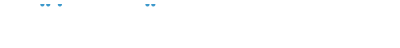
-Graphics-
-Graphics-period 2  
-Graphics-
-Graphics-period 3  
-Graphics-
-Graphics-period 4  
-Graphics-
-Graphics-period 5  
-Graphics-
-Graphics-period 6  
-Graphics-
-Graphics-period 7  
-Graphics-
-Graphics-period 8  
-Graphics-
-Graphics-period 9  
-Graphics-
-Graphics-period 10  
-Graphics-
-Graphics-period 11  
-Graphics-
-Graphics-period 12  -Graphics-
-Graphics-period 13  
-Graphics-
-Graphics-period 14  
-Graphics-
-Graphics-period 15  
-Graphics-
-Graphics-period 16  
-Graphics-
-Graphics-period 17  
-Graphics-
-Graphics-period 18  
-Graphics-
-Graphics-period 19  
-Graphics-
-Graphics-period 20  
-Graphics-period 21

```mathematica
Row[Column[Table[Module[{weightsovertime,improvements,locs,p=i, byyear},
byyear = Catenate[
ReverseSortBy[#,Times@@Dimensions[#MatrixData]&]&/@ 
GatherBy[SortBy[Select[Select[Values[$LifeData],#Class==="Oscillator"&&KeyExistsQ[#,"Period"]&],#Period==p&],#Year&], #Year&]
];weightsovertime=Times@@Dimensions[#MatrixData]&/@byyear;
improvements=FoldList[Function[{min,next},If[next<min,next,min]],Infinity,weightsovertime];
locs=Select[Partition[improvements,2,1],#[[1]]!=#[[2]]&->"Index"];
Labeled[Column[{GraphicsRow[Labeled[CellularAutomatonHistoryPlot["GameOfLife",{#MatrixData,0},#Period,ImageSize->3 Last[2+Dimensions[First@CellularAutomaton["GameOfLife",{#MatrixData,0},#Period]]],Mesh->True,MeshStyle->Opacity[.1]],Text[#Year],BaselinePosition->Top]&/@byyear[[locs]]],NumberLinePlot[Callout[#Year,#Year]&/@SortBy[Select[Select[Values[$LifeData],#Class==="Oscillator"&&KeyExistsQ[#,"Period"]&],#Period==p&],#Year&][[locs]],Axes->None,PlotRange->{1969,2025}]}],Text["period "<>ToString[i]<>"  "],Left]],{i,#}],Dividers->{None,GrayLevel[.8]}]&/@{Range[2,12],Range[13,21]},Spacer[15]]
```

#### New

```mathematica
ClearAll@place
place[currloc_, data_]:= 
Module[{size}, 
size = 2Last[Dimensions[First@CellularAutomaton["GameOfLife",{data["MatrixData"],0},data["Period"]]]];
Sow[Callout[{data["Year"] - 1969, 0}, 
Rotate[Labeled[CellularAutomatonHistoryPlot["GameOfLife", {data["MatrixData"], 0}, data["Period"], ImageSize->10size^(.5),Mesh->True,MeshStyle->Opacity[.1]], data["Year"]], -90Degree], {currloc[[1]] ,currloc[[2]]} ,LeaderSize->{{10,90 °,3}, {3,90°}}, "CalloutStyle"-> Lighter[Gray, .6]
]];
{currloc[[1]] +6size^(.4), currloc[[2]]}]
```

```mathematica
Row[Column[
Table[Module[{weightsovertime,improvements,locs,p=i, byyear},
byyear = Catenate[
ReverseSortBy[#,Times@@Dimensions[#MatrixData]&]&/@ 
GatherBy[SortBy[Select[Select[Values[$LifeData],#Class==="Oscillator"&&KeyExistsQ[#,"Period"]&],#Period==p&],#Year&], #Year&]
];
weightsovertime=Times@@Dimensions[#MatrixData]&/@byyear;
improvements=FoldList[Function[{min,next},If[next<min,next,min]],Infinity,weightsovertime];
locs=Select[Partition[improvements,2,1],#[[1]]!=#[[2]]&->"Index"];
Labeled[ListPlot[r = Reap[f = FoldList[place,{3,8},byyear[[locs]]]][[2]], PlotRange->{{-10,2025 - 1969 + 30}, {-5, 15Max[Differences[f][[All, 1]]]^.55}}, Axes->None, PlotStyle->AbsolutePointSize[5], ImageSize->{250,15Max[Differences[f][[All, 1]]]^.55}, AspectRatio->Full ],Text["period "<>ToString[i]<>"  "],Left]],{i,#}],Dividers->{None,GrayLevel[.8]}, BaselinePosition->Top]&/@{Range[2,11],Range[12,21]},Spacer[10], Alignment->Top]
```

-Graphics-period 2  
-Graphics-period 3  
-Graphics-period 4  
-Graphics-period 5  
-Graphics-period 6  
-Graphics-period 7  
-Graphics-period 8  
-Graphics-period 9  
-Graphics-period 10  
-Graphics-period 11  -Graphics-period 12  
-Graphics-period 13  
-Graphics-period 14  
-Graphics-period 15  
-Graphics-period 16  
-Graphics-period 17  
-Graphics-period 18  
-Graphics-period 19  
-Graphics-period 20  
-Graphics-period 21

### Scratchpad

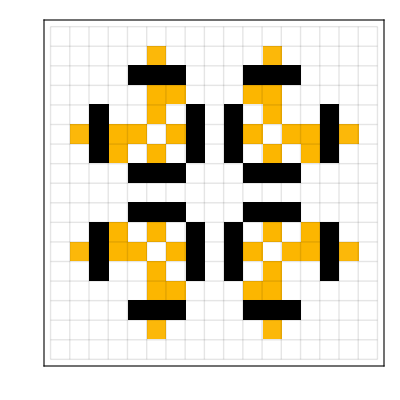
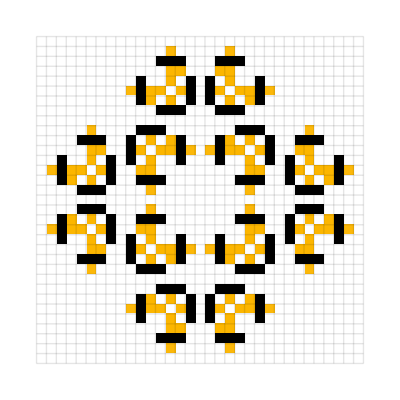
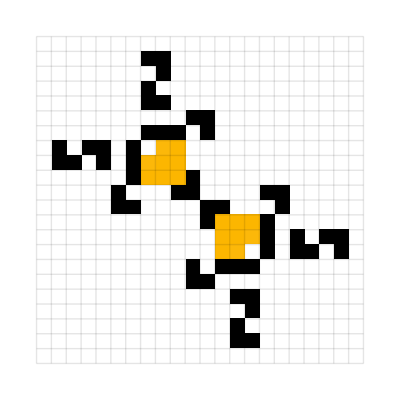
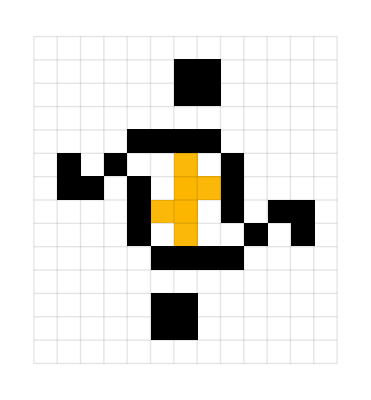
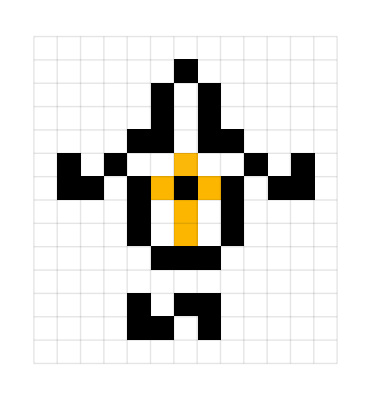
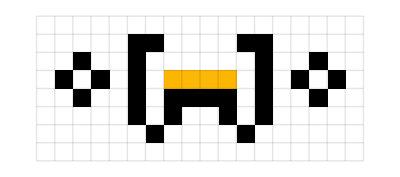
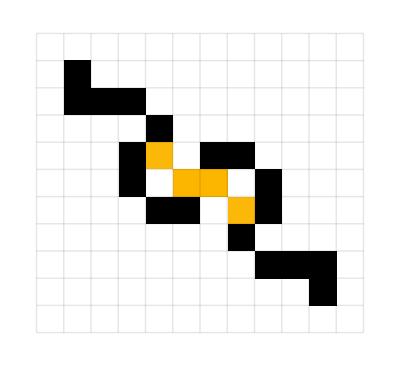
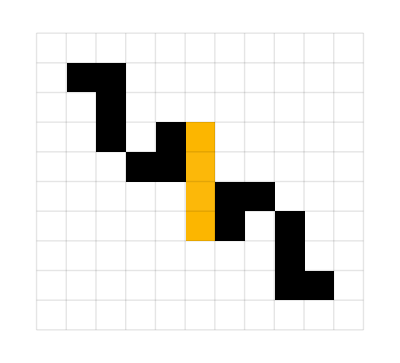
-Graphics-1970-Graphics-1970-Graphics-1971-Graphics-1971-Graphics-1971-Graphics-1971-Graphics-1971-Graphics-1971-Graphics-1971-Graphics-1972-Graphics-1972-Graphics-1972-Graphics-1972-Graphics-1972-Graphics-1972-Graphics-1972-Graphics-1972-Graphics-1972-Graphics-1972-Graphics-1973-Graphics-1973-Graphics-1973-Graphics-1977-Graphics-1982-Graphics-1985-Graphics-1988-Graphics-1989-Graphics-1989-Graphics-1989-Graphics-1989-Graphics-1989-Graphics-1989-Graphics-1989-Graphics-1989-Graphics-1990-Graphics-1993-Graphics-1993-Graphics-1993-Graphics-1993-Graphics-1994-Graphics-1997-Graphics-2003-Graphics-2012-Graphics-2017-Graphics-2018-Graphics-2021-Graphics-2022

```mathematica
Module[{p3=SortBy[Select[$LifeData,#Class==="Oscillator"&&#Period==3&]//Quiet,{#Year,-Times@@Dimensions[#MatrixData]}&],improvements},improvements=Union[FoldList[Function[{min,next},If[Times@@Dimensions[next["MatrixData"]]<Times@@Dimensions[min["MatrixData"]],next,min]],Values[p3]]];
Row[Values[Labeled[CellularAutomatonHistoryPlot["GameOfLife",{#MatrixData,0},6,MeshStyle->Opacity[.1],ImageSize->11 Sqrt[1+Last[Dimensions[#MatrixData]]],Frame->MemberQ[improvements,#],FrameStyle->Directive[Red,Thickness[.05]]],Text[Style[#Year,9,Gray]]]&/@p3],Spacer[1]]]
```

```mathematica
Module[
{p=SortBy[Select[$LifeData,#Class==="Oscillator"&&#Period==9&]//Quiet,{#Year,-Times@@Dimensions[#MatrixData]}&],improvements},improvements=Union[FoldList[Function[{min,next},If[Times@@Dimensions[next["MatrixData"]]<Times@@Dimensions[min["MatrixData"]],next,min]],Values[p]]];
PatternElements[#MatrixData]&/@ improvements
]
```

{<|{{0,0,0,0,0,0,1,1},{0,1,1,0,1,0,0,1},{1,0,1,0,1,0,1,0},{1,0,0,0,1,1,0,0},{0,1,1,1,0,0,0,0},{0,0,0,1,0,0,0,0}}→1,{{1,0,0,1},{1,1,1,1}}→1,{{0,1},{1,1}}→2|>,<|{{0,0,0,1},{0,1,1,1},{1,0,0,0},{1,1,0,0}}→4,{{0,0,1,0,0,0,0,1,0,0},{1,1,0,1,1,1,1,0,1,1},{0,0,1,0,0,0,0,1,0,0}}→1|>,<|{{0,0,0,1},{0,1,1,1},{1,0,0,0},{1,1,0,0}}→4,{{1,1,1,1,1,1}}→1|>}

```mathematica
Sort[%86]
```

{<|{{0,0,0,1},{0,1,1,1},{1,0,0,0},{1,1,0,0}}→4,{{1,1,1,1,1,1}}→1|>,<|{{0,0,0,1},{0,1,1,1},{1,0,0,0},{1,1,0,0}}→4,{{0,0,1,0,0,0,0,1,0,0},{1,1,0,1,1,1,1,0,1,1},{0,0,1,0,0,0,0,1,0,0}}→1|>,<|{{0,0,0,0,0,0,1,1},{0,1,1,0,1,0,0,1},{1,0,1,0,1,0,1,0},{1,0,0,0,1,1,0,0},{0,1,1,1,0,0,0,0},{0,0,0,1,0,0,0,0}}→1,{{1,0,0,1},{1,1,1,1}}→1,{{0,1},{1,1}}→2|>}

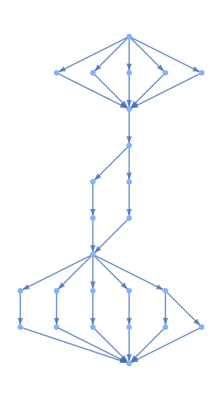

```mathematica
PatternsLayeredGraph[$LifeData["Worker bee"]]
```

```mathematica
SimpleClosure[InitializeMultiwayLife[First[Sort[ResourceFunction["ArrayRotations"][#]]]&[#["MatrixData"]]], If[#2 == -1, Min[#["Period"], 5000], #2]]&[$LifeData["Worker bee"], 1]
```

{<|1→<|Data→{{1,1},{1,11},{2,1},{2,2},{2,3},{2,9},{2,10},{2,11},{3,4},{3,8},{4,3},{4,4},{4,8},{4,9},{6,6},{7,6},{8,6},{9,6},{10,6},{11,6},{13,3},{13,4},{13,8},{13,9},{14,4},{14,8},{15,1},{15,2},{15,3},{15,9},{15,10},{15,11},{16,1},{16,11}},InComponents→{}|>|>,<|2→<|Data→{{1,1},{2,1},{2,2},{2,3},{3,4},{4,3},{4,4}},InComponents→{1}|>,3→<|Data→{{1,11},{2,9},{2,10},{2,11},{3,8},{4,8},{4,9}},InComponents→{1}|>,4→<|Data→{{13,3},{13,4},{14,4},{15,1},{15,2},{15,3},{16,1}},InComponents→{1}|>,5→<|Data→{{13,8},{13,9},{14,8},{15,9},{15,10},{15,11},{16,11}},InComponents→{1}|>,6→<|Data→{{7,5},{7,6},{7,7},{8,5},{8,6},{8,7},{9,5},{9,6},{9,7},{10,5},{10,6},{10,7}},InComponents→{1}|>|>}

```mathematica
Values[Join@@][[All, "Data"]]
```

{{{1,1},{1,11},{2,1},{2,2},{2,3},{2,9},{2,10},{2,11},{3,4},{3,8},{4,3},{4,4},{4,8},{4,9},{6,6},{7,6},{8,6},{9,6},{10,6},{11,6},{13,3},{13,4},{13,8},{13,9},{14,4},{14,8},{15,1},{15,2},{15,3},{15,9},{15,10},{15,11},{16,1},{16,11}},{{1,1},{2,1},{2,2},{2,3},{3,4},{4,3},{4,4}},{{1,11},{2,9},{2,10},{2,11},{3,8},{4,8},{4,9}},{{13,3},{13,4},{14,4},{15,1},{15,2},{15,3},{16,1}},{{13,8},{13,9},{14,8},{15,9},{15,10},{15,11},{16,11}},{{7,5},{7,6},{7,7},{8,5},{8,6},{8,7},{9,5},{9,6},{9,7},{10,5},{10,6},{10,7}}}

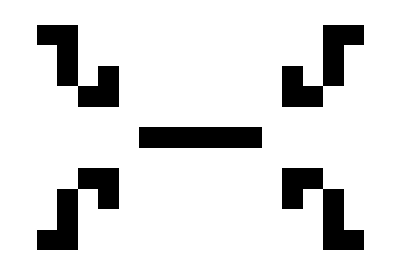
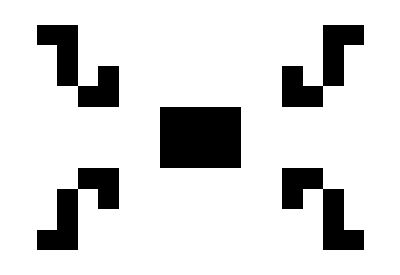

```mathematica
ArrayPlot/@CellularAutomaton["GameOfLife", {$LifeData["Worker bee"]["MatrixData"], 0}, 1]
```

```mathematica
Values[Join@@][[All, "Data"]]
```

{{{1,1},{1,11},{2,1},{2,2},{2,3},{2,9},{2,10},{2,11},{3,4},{3,8},{4,3},{4,4},{4,8},{4,9},{6,6},{7,6},{8,6},{9,6},{10,6},{11,6},{13,3},{13,4},{13,8},{13,9},{14,4},{14,8},{15,1},{15,2},{15,3},{15,9},{15,10},{15,11},{16,1},{16,11}},{{1,1},{2,1},{2,2},{2,3},{3,4},{4,3},{4,4}},{{1,11},{2,9},{2,10},{2,11},{3,8},{4,8},{4,9}},{{13,3},{13,4},{14,4},{15,1},{15,2},{15,3},{16,1}},{{13,8},{13,9},{14,8},{15,9},{15,10},{15,11},{16,11}},{{7,5},{7,6},{7,7},{8,5},{8,6},{8,7},{9,5},{9,6},{9,7},{10,5},{10,6},{10,7}}}

```mathematica
ArrayPad[SparseArray[
Thread[
(Transpose[{#[[All, 1]]  -  Min[#[[All, 1]]]+1, #[[All, 2]] -  Min[#[[All, 2]]]+1}]&[
Ramp[#[[-1]] ]] + 1)->1]], {0, 1}]&/@Values[Join@@][[All, "Data"]]
```

Part::partd1: Depth of object {16,11} is not sufficient for the given part specification.

Part::partd: Part specification {16,11}⟦All,1⟧ is longer than depth of object.

Part::partd1: Depth of object {16,11} is not sufficient for the given part specification.

General::stop: Further output of Part::partd1 will be suppressed during this calculation.

Part::partd: Part specification {16,11}⟦All,2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

{SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…],SparseArray[…]}

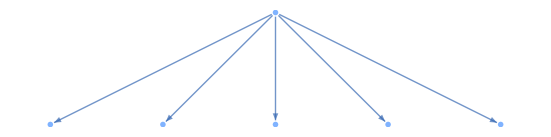

```mathematica
LayeredGraph[LifeMultiwayGraph[%97], VertexShapeFunction->
(With[{sa =
ArrayPad[SparseArray[
Thread[
(Transpose[{#[[All, 1]]  -  Min[#[[All, 1]]]+1, #[[All, 2]] -  Min[#[[All, 2]]]+1}]&[
Ramp[#2[[-1]] ]] + 1)->1]], {0, 1}]}, Inset[
ArrayPlot[sa, Mesh->True,MeshStyle->Opacity[0.1], ImageSize->6Dimensions[sa]], #1]]&)]
```

```mathematica
ArrayPlot[ArrayPad[SparseArray[
Thread[
(Transpose[{#[[All, 1]]  -  Min[#[[All, 1]]]+1, #[[All, 2]] -  Min[#[[All, 2]]]+1}]&[
Ramp[#[[-1]] ]] + 1)->1]], {0, 1}], Mesh-> True]&/@VertexList[%125]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

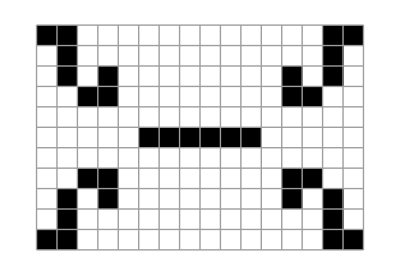
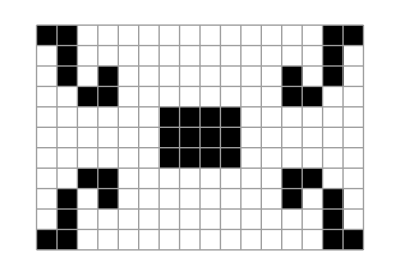

```mathematica
ArrayPlot[#, Mesh-> True]&/@CellularAutomaton["GameOfLife", {$LifeData["Worker bee"]["MatrixData"], 0}, 1]
```

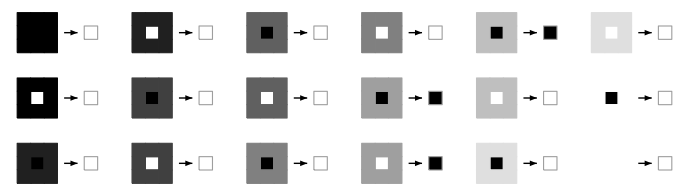

```mathematica
RulePlot[CellularAutomaton["GameOfLife"]]
```

```mathematica
VertexList[%125]
```

{{1,1,{{1,1},{1,11},{2,1},{2,2},{2,3},{2,9},{2,10},{2,11},{3,4},{3,8},{4,3},{4,4},{4,8},{4,9},{6,6},{7,6},{8,6},{9,6},{10,6},{11,6},{13,3},{13,4},{13,8},{13,9},{14,4},{14,8},{15,1},{15,2},{15,3},{15,9},{15,10},{15,11},{16,1},{16,11}}},{2,2,{{1,1},{2,1},{2,2},{2,3},{3,4},{4,3},{4,4}}},{2,3,{{1,11},{2,9},{2,10},{2,11},{3,8},{4,8},{4,9}}},{2,4,{{13,3},{13,4},{14,4},{15,1},{15,2},{15,3},{16,1}}},{2,5,{{13,8},{13,9},{14,8},{15,9},{15,10},{15,11},{16,11}}},{2,6,{{7,5},{7,6},{7,7},{8,5},{8,6},{8,7},{9,5},{9,6},{9,7},{10,5},{10,6},{10,7}}}}

```mathematica
CausalSeparation[framePts_]:=Map[
Union,WeaklyConnectedComponents[
NearestNeighborGraph[framePts,
{All,2Sqrt[2]}]]]
```

```mathematica
CausalSeparation[]
```

```mathematica
InitializeMultiwayLife[First[Sort[ResourceFunction["ArrayRotations"][#]]]&[#["MatrixData"]]]
```

{{1,0,1}}

<|1→<|Data→{{1,0,1}},InComponents→{}|>|>

```mathematica
SimpleClosure[InitializeMultiwayLife[First[Sort[ResourceFunction["ArrayRotations"][#]]]&[#["MatrixData"]]], If[#2 == -1, Min[#["Period"], 5000], #2]]&[$LifeData["Worker bee"], 1]
```

{{1,1},{1,11},{2,1},{2,2},{2,3},{2,9},{2,10},{2,11},{3,4},{3,8},{4,3},{4,4},{4,8},{4,9},{6,6},{7,6},{8,6},{9,6},{10,6},{11,6},{13,3},{13,4},{13,8},{13,9},{14,4},{14,8},{15,1},{15,2},{15,3},{15,9},{15,10},{15,11},{16,1},{16,11}}

{<|1→<|Data→{{1,1},{1,11},{2,1},{2,2},{2,3},{2,9},{2,10},{2,11},{3,4},{3,8},{4,3},{4,4},{4,8},{4,9},{6,6},{7,6},{8,6},{9,6},{10,6},{11,6},{13,3},{13,4},{13,8},{13,9},{14,4},{14,8},{15,1},{15,2},{15,3},{15,9},{15,10},{15,11},{16,1},{16,11}},InComponents→{}|>|>,<|2→<|Data→{{1,1},{2,1},{2,2},{2,3},{3,4},{4,3},{4,4}},InComponents→{1}|>,3→<|Data→{{1,11},{2,9},{2,10},{2,11},{3,8},{4,8},{4,9}},InComponents→{1}|>,4→<|Data→{{13,3},{13,4},{14,4},{15,1},{15,2},{15,3},{16,1}},InComponents→{1}|>,5→<|Data→{{13,8},{13,9},{14,8},{15,9},{15,10},{15,11},{16,11}},InComponents→{1}|>,6→<|Data→{{7,5},{7,6},{7,7},{8,5},{8,6},{8,7},{9,5},{9,6},{9,7},{10,5},{10,6},{10,7}},InComponents→{1}|>|>}

```mathematica
ArrayPlot[SparseArray[Thread[{{1,1},{1,11},{2,1},{2,2},{2,3},{2,9},{2,10},{2,11},{3,4},{3,8},{4,3},{4,4},{4,8},{4,9},{6,6},{7,6},{8,6},{9,6},{10,6},{11,6},{13,3},{13,4},{13,8},{13,9},{14,4},{14,8},{15,1},{15,2},{15,3},{15,9},{15,10},{15,11},{16,1},{16,11}}-> 1]]]
```

-Graphics-

```mathematica
CausalSeparation[{{1,1},{1,11},{2,1},{2,2},{2,3},{2,9},{2,10},{2,11},{3,4},{3,8},{4,3},{4,4},{4,8},{4,9},{6,6},{7,6},{8,6},{9,6},{10,6},{11,6},{13,3},{13,4},{13,8},{13,9},{14,4},{14,8},{15,1},{15,2},{15,3},{15,9},{15,10},{15,11},{16,1},{16,11}}]
```

{{{1,1},{1,11},{2,1},{2,2},{2,3},{2,9},{2,10},{2,11},{3,4},{3,8},{4,3},{4,4},{4,8},{4,9},{6,6},{7,6},{8,6},{9,6},{10,6},{11,6},{13,3},{13,4},{13,8},{13,9},{14,4},{14,8},{15,1},{15,2},{15,3},{15,9},{15,10},{15,11},{16,1},{16,11}}}

```mathematica
VertexList[][[1, -1]] === {{1,1},{1,11},{2,1},{2,2},{2,3},{2,9},{2,10},{2,11},{3,4},{3,8},{4,3},{4,4},{4,8},{4,9},{6,6},{7,6},{8,6},{9,6},{10,6},{11,6},{13,3},{13,4},{13,8},{13,9},{14,4},{14,8},{15,1},{15,2},{15,3},{15,9},{15,10},{15,11},{16,1},{16,11}}
```

True

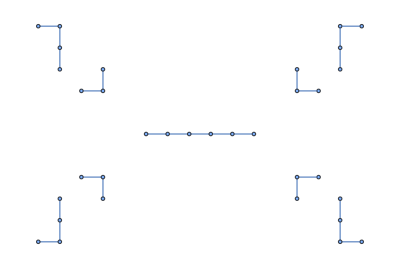

```mathematica
NearestNeighborGraph[{{1,1},{1,11},{2,1},{2,2},{2,3},{2,9},{2,10},{2,11},{3,4},{3,8},{4,3},{4,4},{4,8},{4,9},{6,6},{7,6},{8,6},{9,6},{10,6},{11,6},{13,3},{13,4},{13,8},{13,9},{14,4},{14,8},{15,1},{15,2},{15,3},{15,9},{15,10},{15,11},{16,1},{16,11}}]
```

```mathematica
WeaklyConnectedComponents[]
```

{{{6,6},{7,6},{8,6},{9,6},{10,6},{11,6}},{{15,9},{15,10},{15,11},{16,11}},{{15,1},{15,2},{16,1},{15,3}},{{1,11},{2,11},{2,10},{2,9}},{{1,1},{2,1},{2,2},{2,3}},{{13,8},{13,9},{14,8}},{{13,3},{13,4},{14,4}},{{3,8},{4,8},{4,9}},{{3,4},{4,4},{4,3}}}

```mathematica
$LifeData["Worker bee"]["MatrixData"]["NonzeroPositions"]
```

{{1,1},{1,2},{1,15},{1,16},{2,2},{2,15},{3,2},{3,4},{3,13},{3,15},{4,3},{4,4},{4,13},{4,14},{6,6},{6,7},{6,8},{6,9},{6,10},{6,11},{8,3},{8,4},{8,13},{8,14},{9,2},{9,4},{9,13},{9,15},{10,2},{10,15},{11,1},{11,2},{11,15},{11,16}}

```mathematica
(*SparseArray[#]["NonzeroPositions"]/@*)CellularAutomaton["GameOfLife", {$LifeData["Worker bee"]["MatrixData"], 0}, 1]
```

{{{1,1,0,0,0,0,0,0,0,0,0,0,0,0,1,1},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0},{0,1,0,1,0,0,0,0,0,0,0,0,1,0,1,0},{0,0,1,1,0,0,0,0,0,0,0,0,1,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,1,1,1,1,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,1,0,0,0,0,0,0,0,0,1,1,0,0},{0,1,0,1,0,0,0,0,0,0,0,0,1,0,1,0},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0},{1,1,0,0,0,0,0,0,0,0,0,0,0,0,1,1}},{{1,1,0,0,0,0,0,0,0,0,0,0,0,0,1,1},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0},{0,1,0,1,0,0,0,0,0,0,0,0,1,0,1,0},{0,0,1,1,0,0,0,0,0,0,0,0,1,1,0,0},{0,0,0,0,0,0,1,1,1,1,0,0,0,0,0,0},{0,0,0,0,0,0,1,1,1,1,0,0,0,0,0,0},{0,0,0,0,0,0,1,1,1,1,0,0,0,0,0,0},{0,0,1,1,0,0,0,0,0,0,0,0,1,1,0,0},{0,1,0,1,0,0,0,0,0,0,0,0,1,0,1,0},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0},{1,1,0,0,0,0,0,0,0,0,0,0,0,0,1,1}}}

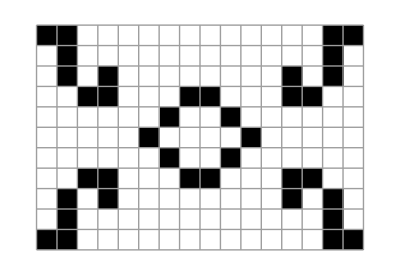
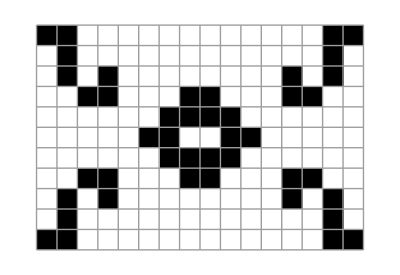
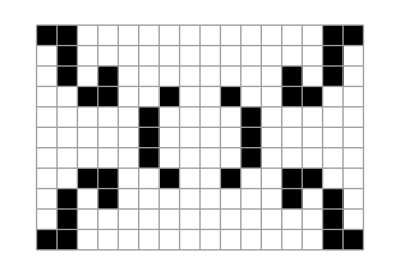
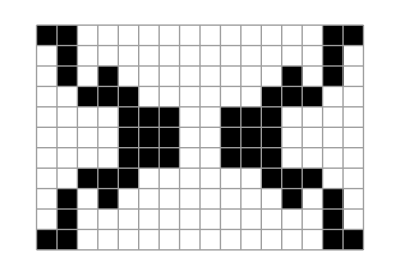
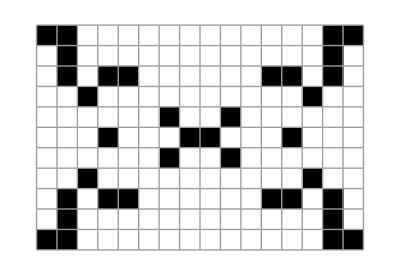
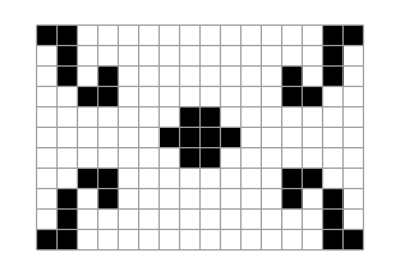
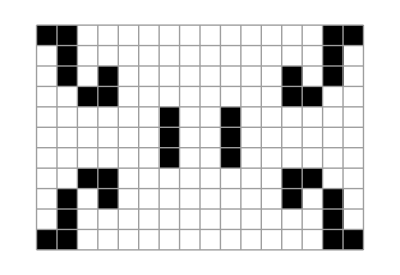
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ArrayPlot[#, Mesh-> True]&/@CellularAutomaton["GameOfLife", {$LifeData["Worker bee"]["MatrixData"], 0}, 9]
```

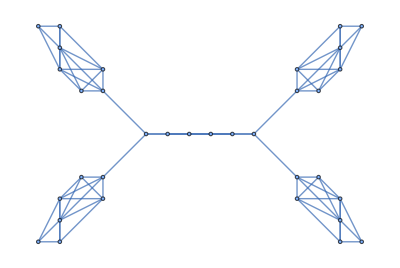
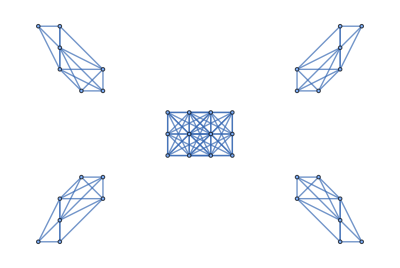
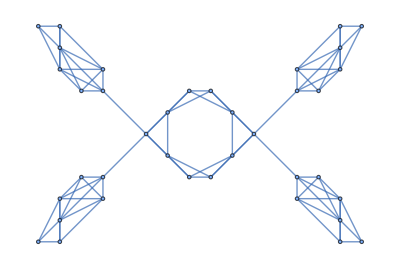
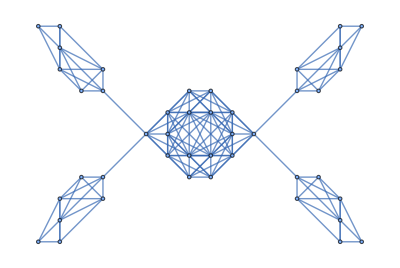
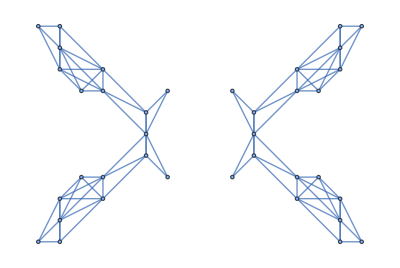
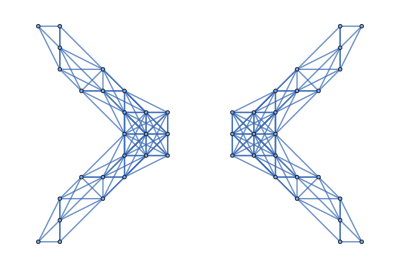
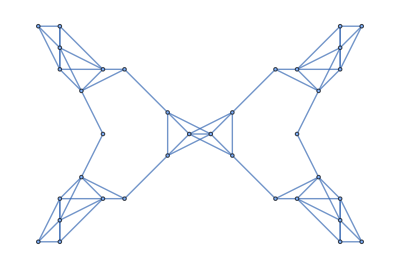
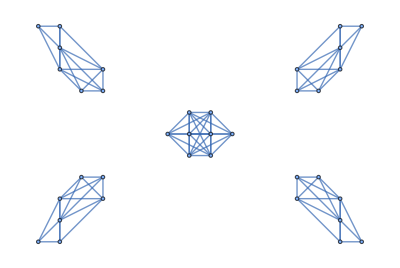
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
NearestNeighborGraph[Position[Transpose[
Reverse[Normal[#]]],1], {All,2Sqrt[2]}]&/@CellularAutomaton["GameOfLife", {$LifeData["Worker bee"]["MatrixData"], 0}, 9]
```

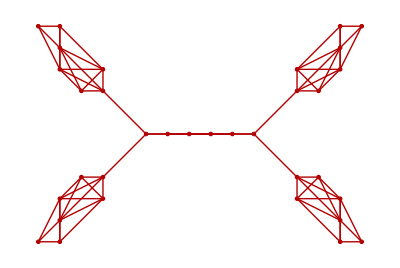
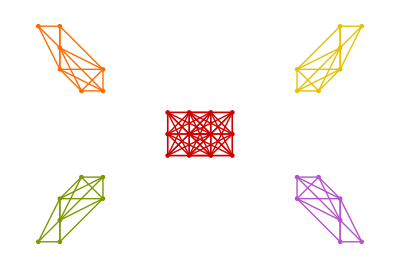
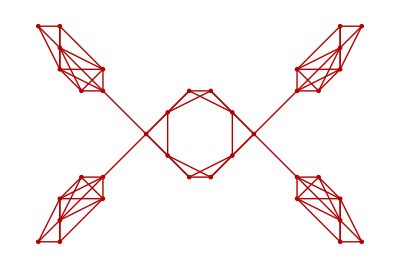
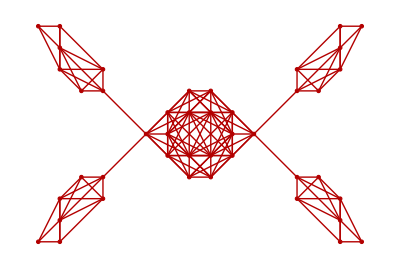
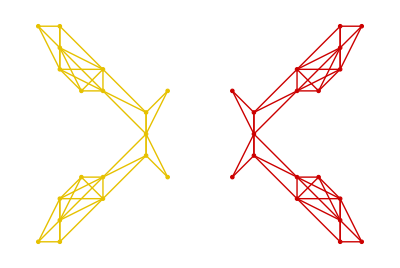
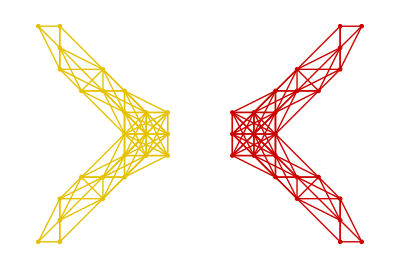
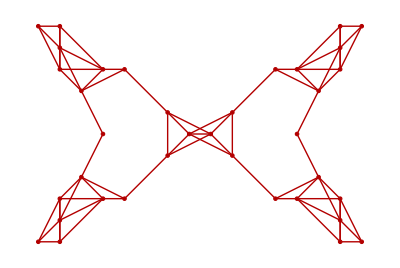
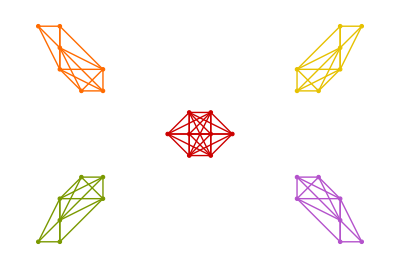
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
With[{ng = NearestNeighborGraph[Position[Transpose[
Reverse[Normal[#]]],1], {All,2Sqrt[2]}]}, HighlightGraph[ng, (Subgraph[ng,#]&/@ WeaklyConnectedComponents[ng])]]&/@CellularAutomaton["GameOfLife", {$LifeData["Worker bee"]["MatrixData"], 0}, 9]
```

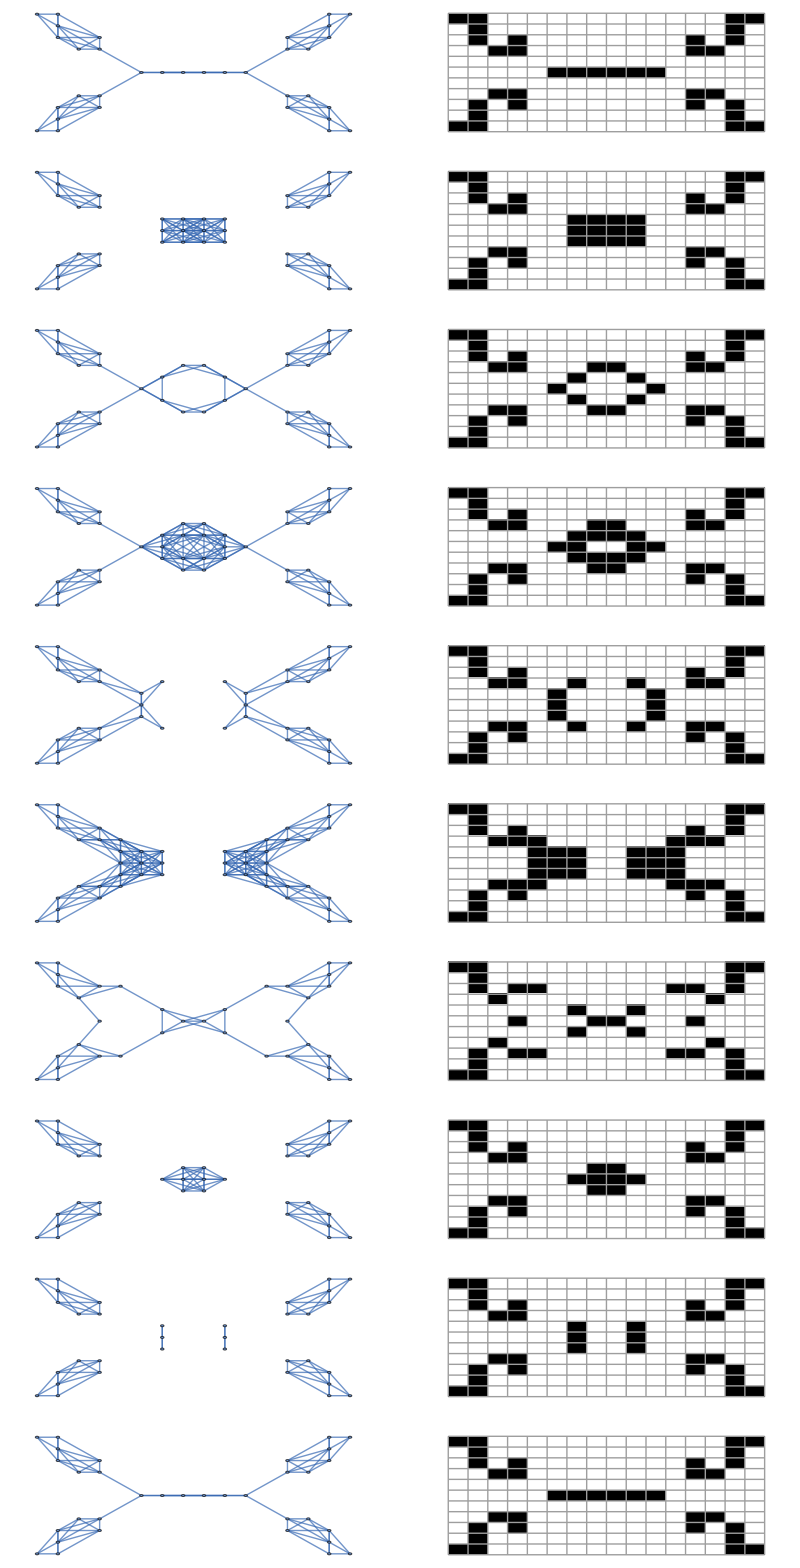
-Graphics--Graphics-

```mathematica
Row[{GraphicsGrid[Transpose[{With[{ng = NearestNeighborGraph[Position[Transpose[
Reverse[Normal[#]]],1], {All,2Sqrt[2]}]}, HighlightGraph[ng, (Subgraph[ng,#]&/@ WeaklyConnectedComponents[ng])]]&/@CellularAutomaton["GameOfLife", {$LifeData["Worker bee"]["MatrixData"], 0}, 9], ArrayPlot[#, Mesh-> True]&/@CellularAutomaton["GameOfLife", {$LifeData["Worker bee"]["MatrixData"], 0}, 9]}]], PatternsLayeredGraph[$LifeData["Worker bee"]]}]
```

```mathematica
PatternsLayeredGraph[$LifeData["Worker bee"]]
```

-Graphics-

```mathematica
PatternsLayeredGraph[$LifeData["Worker bee"]]
```

-Graphics-

```mathematica
IterateMultiwayLife[state_]:=Module[{
nextState=state,
max=Max[Keys[state]],
frame,sep,keep,new
},
nextState=Map[MapAt[IterateLife,#,"Data"]&,nextState];
frame=Apply[Union,#Data&/@Values[nextState]];
sep=CausalSeparation[frame];
keep=Select[nextState,MemberQ[sep,#Data]&];
new=Complement[sep,#Data&/@Values[keep]];
keep=KeyValueMap[CompoundExpression[max++,
max->ReplacePart[#2,"InComponents"->{#1}]
]&,keep];
new=Map[Function[pts,
CompoundExpression[max++,
max->Association[
"Data"->pts,
"InComponents"->Keys[Select[nextState,
IntersectingQ[pts,#Data]&]]
]
]],new];
Association[Join[keep,new]]
]
```

### Rotating patternslayeredgraph verts

```mathematica
ArrayPlot[ArrayPad[SparseArray[
Thread[
(Transpose[Reverse@{Echo[#[[All, 1]]  -  Min[#[[All, 1]]]+1], #[[All, 2]] -  Min[#[[All, 2]]]+1}]&[
Ramp[#[[-1]]]] + 1)->1]], {0, 1}]]&/@VertexList[PatternsLayeredGraph[$LifeData["Worker bee"]] ][[{1}]]
```

{1,1,2,2,2,2,2,2,3,3,4,4,4,4,6,7,8,9,10,11,13,13,13,13,14,14,15,15,15,15,15,15,16,16}

{-Graphics-}

```mathematica
VertexShapeFunction->
(With[{sa =
ArrayPad[SparseArray[
Thread[
(Transpose[{#[[All, 1]]  -  Min[#[[All, 1]]]+1, #[[All, 2]] -  Min[#[[All, 2]]]+1}]&[
Ramp[#2[[-1]] ]] + 1)->1]], {0, 1}]}, Inset[
ArrayPlot[sa, Mesh->True,MeshStyle->Opacity[0.1], ImageSize->3Dimensions[sa]], #1]]&)
```